```mathematica
(*** DATA-DRIVEN PREDICTIONS for RF detector ***)
```

```mathematica
(** FNR **) 
(* test if data is there *)
```

```mathematica
getMonValues[dataDirPathForSeshNumPostCorr[All], "FPR",11]
```

{0.189048,0.270127,0.342801,0.409231,0.469308,0.523021,0.571181,0.613939,0.652491,0.687322,0.7186,0.746941,0.772036,0.795329,0.816313,0.834639,0.851623,0.866614,0.880062,0.892301,0.903391,0.913582,0.922356,0.930144,0.937203,0.943659,0.949452,0.954618,0.959474,0.963681}

{0.189048,0.270127,0.342801,0.409231,0.469308,0.523021,0.571181,0.613939,0.652491,0.687322,0.7186,0.746941,0.772036,0.795329,0.816313,0.834639,0.851623,0.866614,0.880062,0.892301,0.903391,0.913582,0.922356,0.930144,0.937203,0.943659,0.949452,0.954618,0.959474}

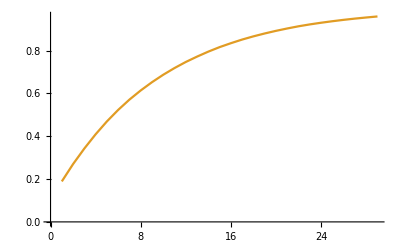

```mathematica
(* EMPIRICAL *) 
(* all sessions 4-7 *) 
getMonValues[dataDirPathForSeshNum[All], "FPR",11]
estRfFNRChartSesh4567 = ListLinePlot[Inner[List, Range[1,29], getMonValues[dataDirPathForSeshNum[All], "FPR",11], List], PlotStyle->{ColorData[97,"ColorList"][[2]](*Darker@Blue,Dotted*)}(*, PlotLegends->{"Data estimate (7.7 hrs)"}*)]
```

```mathematica
(*** APPROACH PREDICTIONS ***)
```

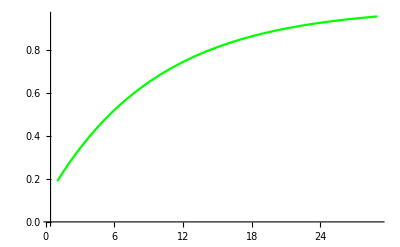

```mathematica
(* updated *) 
gtRfFPRChart =ListLinePlot[ {#, Simplify@predRfMonFPRTheor[0.1, #]}& /@ Table[n, {n,1,29, 1}], 
PlotStyle->Green, (*PlotLegends->{"Ground-truth FPR"},*) PlotRange->All]
```

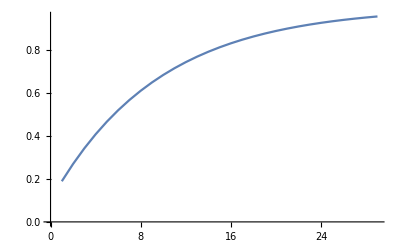

```mathematica
(* automated for sessions 4-7, det fnr = 0.09959699010793902 *) 
predRfFNRchartSesh4567 = ListLinePlot[Inner[List, Range[1,29], predRfMonFPRTheor[countFromFiles[ "FNcount",detFilenames[fullTripleList[{4,5,6,7}]]]/countFromFiles[ "h1count",detFilenames[fullTripleList[{4,5,6,7}]]],#]&/@ Range[1,29], List], PlotStyle->{ColorData[97,"ColorList"][[1]](*Darker@Magenta,Dashed*)}(*, PlotLegends->{"Our prediction (7.7 hrs)"}*)]
```

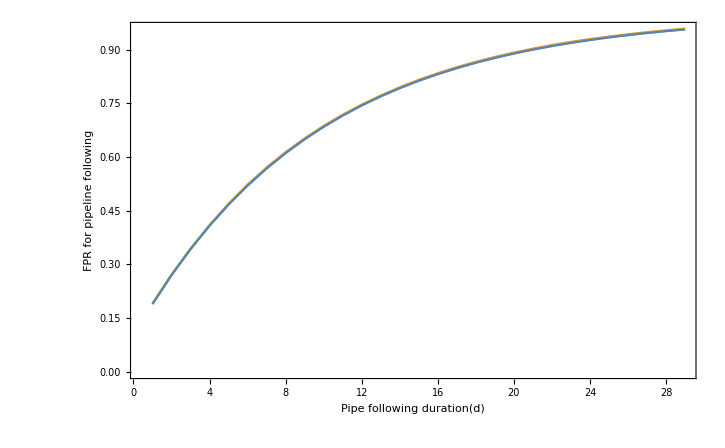

```mathematica
(* POST-CORRECTION *) 
Show[gtRfFPRChart,estRfFNRChartSesh4567, predRfFNRchartSesh4567,(*PlotLabel->"Bhah",  AxesLabel -> {"Monitor window size", "Monitor FPR"}*)Frame->True, FrameLabel->{StringJoin["Pipe following duration", ToString[ Style["(d)", Italic], StandardForm] ],"FPR for pipeline following"}, ImageSize->500, BaseStyle-> {FontSize->15}]
```

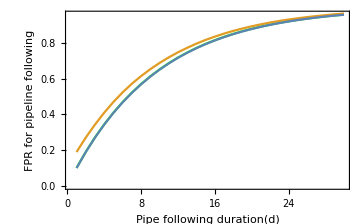
```mathematica
(* old: *)  
-Graphics-
```